### Required Funcs

```mathematica
(* Produces a region from the parametrized border {f,g},{umin,umax};
-f,g are the *heads* of the border functions *)
parametricregion[{{f_,g_},{umin_,umax_}}]:=Module[{pts,plot},
plot=ParametricPlot[{f[u],g[u]},{u,umin,umax}];
pts=Flatten[Table[plot[[1,1,3,i,1]],{i,2,Length[Position[plot,Line]]+1}],1];
pts=DeleteDuplicates[pts];
BoundaryMeshRegion[pts,Line[Join[Range[Length[pts]-1],{1}]]]];

(* Determines the eigensystem up to Num'th eigenvalue for the given region 
Returns {freqlist,funclist}*)
egsystem[Num_,const_:1][region_]:=Module[{f,freqs,vals,funcs}, {vals,funcs}=NDEigensystem[{-const Laplacian[f[x,y],{x,y}],DirichletCondition[f[x,y]==0,True]},{f},{x,y}∈region,Num];
freqs=√vals;
{freqs,funcs}];

(* functionlist is list of 2D functions that are over region *)
reimannianapprox[region_,numberdiv_:50][functionlist_]:=Module[{Δx,Δy,area,squaregrid,i,inside,heights,xmin,xmax,ymax,ymin,coord},
coord=region["Coordinates"];
xmax=Max[coord[[All,1]]];
xmin=Min[coord[[All,1]]];
ymax=Max[coord[[All,2]]];
ymin=Min[coord[[All,2]]];
Δx=(xmax-xmin)/numberdiv;
Δy=(ymax-ymin)/numberdiv;
area=Δx*Δy;
squaregrid=Flatten[Table[{x,y},
{x,xmin,xmax,Δx},
{y,ymin,ymax,Δy}],1];
inside={};
For[i=1,i≤Length[squaregrid],i++,
If[RegionMember[region,squaregrid[[i]]],
AppendTo[inside,squaregrid[[i]]],
False]];
heights=Table[Map[functionlist[[i]][#[[1]],#[[2]]]&,inside],{i,Length[functionlist]}];
area*Map[Total,heights]]
```

## “Integral”

```mathematica
wp=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/Weird Shape.m"];
wreg=parametricregion[wp];
wsys=egsystem[30][wreg];
```

```mathematica
bigcreg=DiscretizeRegion[Disk[{0,0},385/2]];
bigcsys=egsystem[30][bigcreg];
```

#### Using NIntegrate

```mathematica
fastintegral[interpolation_]:=NIntegrate[interpolation[x,y],{x,y}∈interpolation["ElementMesh"],Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
RepeatedTiming[fastintegral[wsys[[2,2]]]]
```

{0.756,-0.129423}

```mathematica
RepeatedTiming[fastintegral[wsys[[2,#]]]&/@Range[5]]
```

{3.85,{-0.861569,-0.129423,-0.194507,0.357675,0.248136}}

#### Using “ElementMesh”

```mathematica
Timing[Module[{areas,coordinates,trilist,onetri,centroids,values},areas=wsys[[2,2]]["ElementMesh"]["MeshElementMeasure"][[1]];
coordinates=wsys[[2,2]]["Grid"];
trilist=wsys[[2,2]]["ElementMesh"]["MeshElements"][[1,1]];
onetri[i_]:=trilist[[i,1;;3]];
centroids=Table[RegionCentroid[BoundaryMeshRegion[coordinates[[#]]&/@onetri[i],Line[{1,2,3,1}]]],{i,Length[trilist]}];
values=Table[wsys[[2,2]][centroids[[i,1]],centroids[[i,2]]],{i,Length[centroids]}];
values.areas]]
```

{7.99935,-0.130051}

#### Using a square grid

```mathematica
(* functionlist is list of 2D functions that are over region *)
reimannianapprox[region_,numberdiv_:50][functionlist_]:=Module[{Δx,Δy,area,squaregrid,i,inside,heights,xmin,xmax,ymax,ymin,coord},
coord=region["Coordinates"];
xmax=Max[coord[[All,1]]];
xmin=Min[coord[[All,1]]];
ymax=Max[coord[[All,2]]];
ymin=Min[coord[[All,2]]];
Δx=(xmax-xmin)/numberdiv;
Δy=(ymax-ymin)/numberdiv;
area=Δx*Δy;
squaregrid=Flatten[Table[{x,y},
{x,xmin,xmax,Δx},
{y,ymin,ymax,Δy}],1];
inside={};
For[i=1,i≤Length[squaregrid],i++,
If[RegionMember[region,squaregrid[[i]]],
AppendTo[inside,squaregrid[[i]]],
False]];
heights=Table[Map[functionlist[[i]][#[[1]],#[[2]]]&,inside],{i,Length[functionlist]}];
area*Map[Total,heights]]
```

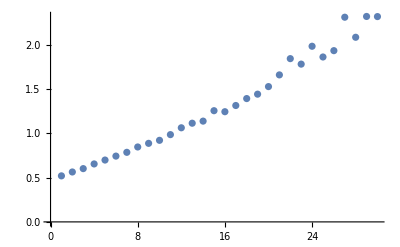

```mathematica
ListPlot[Table[
{i,RepeatedTiming[fastapprox[wreg,100][wsys[[2,1;;i]]]][[1]]},{i,Length[wsys[[2]]]}]]
```

#### Using Quadratic-Order Triangle Rule

Answer here: http://mathematica.stackexchange.com/questions/120733/approximating-integral-under-2d-interpolation-function/120839#120839 gives proof that it is as accurate as the NIntegrate method I have been using.

```mathematica
QOtriangleApprox[efunclist_]:=Module[{emesh,indices},
emesh=efunclist[[1]]["ElementMesh"];
indices=emesh["MeshElements"]/.{NDSolve`FEM`TriangleElement[t_]}:>Flatten@t[[All,4;;6]];
Table[
Total[Total[Partition[eigenfunction["ValuesOnGrid"][[indices]],3],{2}]*
First@eigenfunction["ElementMesh"]["MeshElementMeasure"]/3],
{eigenfunction,efunclist}]]
```

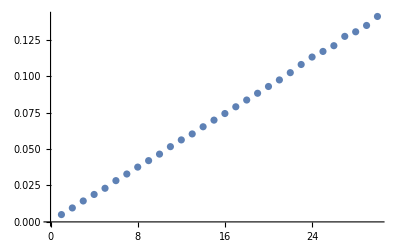

```mathematica
ListPlot[Table[
{i,RepeatedTiming[QOtriangleApprox[wsys[[2,1;;i]]]][[1]]},
{i,Length[wsys[[2]]]}]]
```

#### Comparison Values

```mathematica
qotri=QOtriangleApprox[wsys[[2]]];
precise=Table[fastintegral[wsys[[2,i]]],{i,Length[wsys[[2]]]}];
```

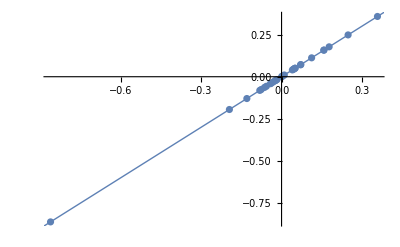

```mathematica
Show[ListPlot[Table[{precise[[i]],qotri[[i]]},{i,Length[qotri]}],PlotRange->All],
Plot[x,{x,-1,1},PlotStyle->Thin]]
```

#### Comparison Timing

```mathematica
RepeatedTiming[QOtriangleApprox[wsys[[2]]]]
RepeatedTiming[Table[fastintegral[wsys[[2,i]]],{i,Length[wsys[[2]]]}]]
```

{0.15,{-0.861569,-0.129423,-0.194507,0.357675,0.248136,0.0706918,0.050766,0.157744,0.112112,0.0101853,0.0454705,-0.0221128,0.177402,-0.023759,-0.0416631,-0.0637416,-0.075995,-0.0811182,-0.0566582,0.0039306,0.040421,-0.0169356,0.000372212,-0.0383144,0.157976,-0.0312862,0.0457318,0.0498541,0.0720455,0.00274389}}

{22.,{-0.861569,-0.129423,-0.194507,0.357675,0.248136,0.0706918,0.050766,0.157744,0.112112,0.0101853,0.0454705,-0.0221128,0.177402,-0.023759,-0.0416631,-0.0637416,-0.075995,-0.0811182,-0.0566582,0.0039306,0.040421,-0.0169356,0.000372212,-0.0383144,0.157976,-0.0312862,0.0457318,0.0498541,0.0720455,0.00274389}}

```mathematica
timingQO=Table[RepeatedTiming[QOtriangleApprox[wsys[[2,1;;i]]]][[1]],{i,Length[wsys[[2]]]}]
timingPre=RepeatedTiming[Table[fastintegral[wsys[[2,i]]],{i,#}]][[1]]&/@Range[Length[wsys[[2]]]]
```

{0.0049,0.0096,0.015,0.0188,0.0229,0.0278,0.0325,0.0371,0.042,0.0466,0.052,0.0558,0.06,0.066,0.073,0.077,0.08,0.0868,0.0886,0.093,0.0976,0.1,0.11,0.11,0.12,0.12,0.13,0.14,0.15,0.14}

{0.74,1.45,2.19,2.89,3.617,4.32,5.076,5.87,6.7,7.266,8.029,8.652,10.,10.7,11.,11.66,12.46,13.1,13.94,14.9,15.5,17.,17.,18.,18.,19.4,19.,21.2,21.8,23.}

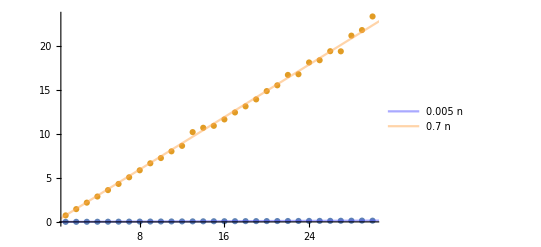

```mathematica
tQOfit[x_]:=Evaluate[Fit[timingQO,{x},x]]
tPrefit[x_]:=Evaluate[Fit[timingPre,{x},x]]
Show[ListPlot[{timingQO,timingPre},PlotRange->All],
Plot[Legended[tQOfit[x],tQOfit[n]],{x,0,40},PlotStyle->{Lighter[Blue],Opacity[0.5]}],
Plot[Legended[tPrefit[x],tPrefit[n]],{x,0,40},PlotStyle->{Lighter[Orange],Opacity[0.5]}]]
```

## Throwing Away Frequencies

The idea is that sound is percieved as a pressure wave and so if the eigenfunction ‘cancels’ itself out when attempting to make a pressure wave (the integral underneath is close to or exactly 0), that eigenfunction will not produce a very intense frequency, so its frequency can be ignored.
The keep function is supposed to decide, given an eigenfunction, whether or not its frequency is supposed to be kept.

```mathematica
(* Returns list: True if Keep and False if Not Keep;
Requires eigenfunctions to be the head of funciton over region; *)
keep[eigenfunctionlist_,threshhold_:0.1]:=Module[{ints,keeplist,i},
ints=Abs[QOtriangleApprox[eigenfunctionlist]];
keeplist={};
For[i=1,i≤Length[eigenfunctionlist],i++,
If[ints[[i]]≥threshhold,
AppendTo[keeplist,True],
AppendTo[keeplist,False]]];
keeplist]
```

```mathematica
keep[bigcsys[[2]],bigcreg]
```

{True,False,False,False,False,True,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,True,True,True}

The loudfreqs function, given an eigensystem and its region, outputs a list of frequencies that should produce a sound.

```mathematica
(* fre and fun are lists of eigenfrequencies and eigenfunctions correspondingly;
Returns list of indices of frequencies to keep *)
loudfreqs[fun_,threshhold_:0.1]:=Module[{decision,keeps,i},
decision=keep[fun,threshhold];
keeps={};
For[i=1,i≤Length[fun],i++,
If[decision[[i]],
AppendTo[keeps,i];,
False;]];
keeps];
```

```mathematica
loudfreqs[bigcsys[[2]],bigcreg,25]
```

{1,6,15,30}

The graphweight function outputs a ListPlot of frequency number against its approximate integral. Will be helpful in determining an appropriate threshhold for a certain shape.

```mathematica
graphweight[fun_]:=Module[{},
Clear[ints,lp,thp];
ints=Abs[QOtriangleApprox[fun]];
lp=ListPlot[ints,PlotRange->All];
thp[t_]:=Plot[t,{x,0,Length[ints]+5},Filling->Axis,FillingStyle->Opacity[0.2],PlotStyle->Thin];
Manipulate[Show[lp,thp[threshhold]],{threshhold,0,Max[ints],(Max[ints]-Min[ints])/100}]]
```

```mathematica
graphweight[bigcsys[[2]],bigcreg]
DynamicModule[{threshhold=50},Show[lp,thp[threshhold]]]
```

The colorfreqs function outputs color list for whether certain frequencies should be kept or not. This can be used with Graphics to produce the vertical lines for each frequency.

```mathematica
(* Keep is Red, Throw away is Blue *)
colorfreqs[fun_,threshhold_:0]:=Module[{decision,color},
decision=keep[fun,threshhold];
Table[If[decision[[i]],Red,Blue],{i,Length[fun]}]];

(* Returns the options necessary to input into Graphics[] *)
freqband[min_,max_,color_:Red]:=Module[{ave,thickness},
ave=Mean[{min,max}];
thickness=(min-max)/2;
{color,Thickness[thickness],Opacity[0.5],InfiniteLine[{ave,0},{0,1}]}];

freqlines[minsystem_,maxsystem_:{},threshhold_:0]:=Module[{color,lines},
color=colorfreqs[minsystem[[2]],threshhold];
lines[i_]:=If[Length[maxsystem]==0,
{color[[i]],Thin,Infinity[{minsystem[[1,i]]},{0,1}]},freqband[minsystem[[1,i]],maxsystem[[1,i]],color[[i]]]];
Graphics[Table[lines[i],{i,Length[minsystem[[1]]]}],PlotRange->{{0,Max[minsystem[[1]]]*1.1},{0,Max[minsystem[[1]]]*0.25}},Frame->True]]
```

### Test on Non-Circular Shape

```mathematica
wp=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/Weird Shape.m"];
wreg=parametricregion[wp];
wsys=egsystem[30][wreg];
```

```mathematica
graphweight[wsys[[2]],wreg]
DynamicModule[{threshhold=0.141393},Show[lp,thp[threshhold]]]
```

```mathematica
wsys[[1,#]]&/@loudfreqs[wsys[[2]],wreg,0.141393]
```

{4.42056,6.90659,7.8205,8.83506,10.8599,13.1313,17.5848}